```mathematica
Show[Plot[f[x],{x,-5,5}],Plot[f'[x],{x,-5,5},PlotStyle->Green],Plot[f''[x],{x,-5,5},PlotStyle->Red]]
```

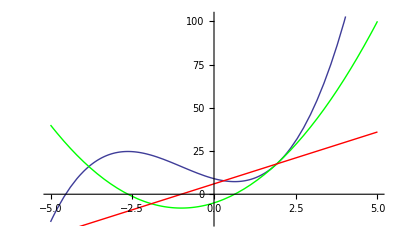

```mathematica
f[x_]:=x^3+3 x^2-5x+9;
```

```mathematica
f[x_]=x^3+3 x^2-5x+9;
Newt[z_]=z-f[z]/f'[z];
ListDensityPlot[Table[-Length[FixedPointList[Newt,N[a+b I],30]],{b,-2,2,.01},{a,-2,2,.01}],Mesh->False,MeshRange->{{-2,2},{-2,2}}]
```

-Graphics-